Petrov Galerkin bilinear space time weights using standard shape functions:
1/(12Δt)[(ϕ_(i-1)^(n+1)-ϕ_(i-1)^n)+4(ϕ_i^(n+1)-ϕ_i^n)+(ϕ_(i+1)^(n+1)-ϕ_(i+1)^n)] - α/(8Δt)[(ϕ_(i+1)^(n+1)-ϕ_(i+1)^n)-(ϕ_(i-1)^(n+1)-ϕ_(i-1)^n)]
- β/(8Δt)[(ϕ_(i+1)^(n+1)-ϕ_(i+1)^n)-(ϕ_(i-1)^(n+1)-ϕ_(i-1)^n)]+u/(6h)(ϕ_(i+1)^(n+1)-ϕ_(i-1)^(n+1)) - (α u)/(6h)(ϕ_(i-1)^(n+1)-2 ϕ_i^(n+1)+ϕ_(i+1)^(n+1))
-βu/(8h)(ϕ_(i-1)^(n+1)-2 ϕ_i^(n+1)+ϕ_(i+1)^(n+1))+ u/(12h)(ϕ_(i+1)^n-ϕ_(i-1)^n) -(α u)/(12h)(ϕ_(i-1)^n-2 ϕ_i^n+ϕ_(i+1)^n)
-βu/(8h)(ϕ_(i-1)^n-2 ϕ_i^n+ϕ_(i+1)^n)-K/(3 h^2)(ϕ_(i-1)^(n+1)-2 ϕ_i^(n+1)+ϕ_(i+1)^(n+1))+1/2(ϕ_(i-1)^n-2 ϕ_i^n+ϕ_(i+1)^n)] = 0

## Analytical example:

```mathematica
Clear["Global`*"]
```

```mathematica
ϕ0[x_]:= Exp[-(x-u)^2/(4 K)];
ϕ[x_,t_]:= 1/(Sqrt[1+t]) Exp[-(x-u(t+1))^2/(4 K (t+1))];
```

```mathematica
u=0.25; K=0.00125;
```

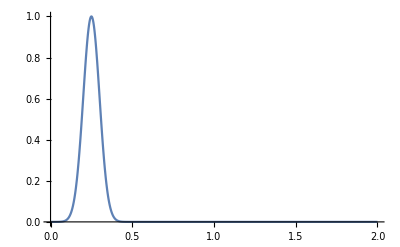

```mathematica
Plot[ϕ0[x],{x,0,2},PlotRange->All]
```

Solution after 1s should move 0.25 on the right:

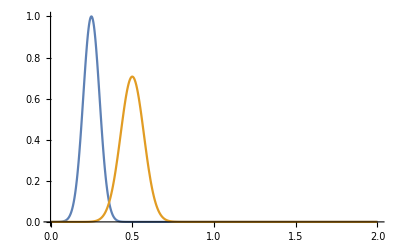

```mathematica
Plot[{ϕ[x,0],ϕ[x,1]},{x,0,2},PlotRange->All]
```

Numerical example:

```mathematica
Δt = 0.05;M=40; Δx = L / M; L=2; u= 0.25; γ=u Δx/K; c=u Δt/Δx;
```

```mathematica
ϕn[0,n_]:=0;ϕn[M,n_]:=0;
```

```mathematica
sol[0] = Table[ϕn[j,0]->ϕ0[j Δx],{j,1,M-1}]
```

{ϕn[1,0]→0.000335463,ϕn[2,0]→0.011109,ϕn[3,0]→0.135335,ϕn[4,0]→0.606531,ϕn[5,0]→1.,ϕn[6,0]→0.606531,ϕn[7,0]→0.135335,ϕn[8,0]→0.011109,ϕn[9,0]→0.000335463,ϕn[10,0]→3.72665×10^-6,ϕn[11,0]→1.523×10^-8,ϕn[12,0]→2.28973×10^-11,ϕn[13,0]→1.26642×10^-14,ϕn[14,0]→2.57676×10^-18,ϕn[15,0]→1.92875×10^-22,ϕn[16,0]→5.31109×10^-27,ϕn[17,0]→5.38019×10^-32,ϕn[18,0]→2.00501×10^-37,ϕn[19,0]→2.74879×10^-43,ϕn[20,0]→1.38634×10^-49,ϕn[21,0]→2.57221×10^-56,ϕn[22,0]→1.75569×10^-63,ϕn[23,0]→4.40853×10^-71,ϕn[24,0]→4.07236×10^-79,ϕn[25,0]→1.3839×10^-87,ϕn[26,0]→1.73008×10^-96,ϕn[27,0]→7.95674×10^-106,ϕn[28,0]→1.3462×10^-115,ϕn[29,0]→8.37894×10^-126,ϕn[30,0]→1.91856×10^-136,ϕn[31,0]→1.61609×10^-147,ϕn[32,0]→5.00797×10^-159,ϕn[33,0]→5.70904×10^-171,ϕn[34,0]→2.39425×10^-183,ϕn[35,0]→3.69388×10^-196,ϕn[36,0]→2.09653×10^-209,ϕn[37,0]→4.37749×10^-223,ϕn[38,0]→3.36244×10^-237,ϕn[39,0]→9.50144×10^-252}

```mathematica
α = 6/(γ c)(Coth[γ/2]-2/γ); β=(1-6/(γ c))(Coth[γ/2]-2/γ); (*α=0; β=0;*)
```

```mathematica
Clear[n,vars,eqns];
```

```mathematica
sol[n_]:=Module[{vars,eqns},
(*define the variables*)
vars = Table[ϕn[j,n],{j,1,M-1}];
(* define equations substituting for the values ϕn determined at last timestep*)
eqns = Table[1/(12Δt)((ϕn[j-1,n]-ϕn[j-1,n-1])+4(ϕn[j,n]-ϕn[j,n-1])+(ϕn[j+1,n]-ϕn[j+1,n-1]))-α/(8Δt)((ϕn[j+1,n]-ϕn[j+1,n-1])-(ϕn[j-1,n]-ϕn[j-1,n-1]))-β/(8Δt)((ϕn[j+1,n]-ϕn[j+1,n-1])-(ϕn[j-1,n]-ϕn[j-1,n-1]))+u/(6Δx)(ϕn[j+1,n]-ϕn[j-1,n])-(α u)/(6Δx)(ϕn[j-1,n]-2ϕn[j,n]+ϕn[j+1,n])-(β u)/(8Δx)(ϕn[j-1,n]-2ϕn[j,n]+ϕn[j+1,n])+u/(12Δx)(ϕn[j+1,n-1]-ϕn[j-1,n-1])-(α u)/(12Δx)(ϕn[j-1,n-1]-2ϕn[j,n-1]+ϕn[j+1,n-1])-(β u)/(8Δx)(ϕn[j-1,n-1]-2ϕn[j,n-1]+ϕn[j+1,n-1])-K/(3 Δx^2)((ϕn[j-1,n]-2ϕn[j,n]+ϕn[j+1,n])+1/2(ϕn[j-1,n-1]-2ϕn[j,n-1]+ϕn[j+1,n-1]))==0
,{j,1,M-1}]/.sol[n-1];
(*solve the equations*)
Solve[eqns,vars][[1]]]
```

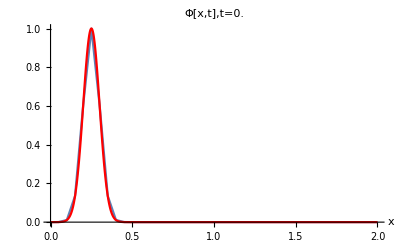
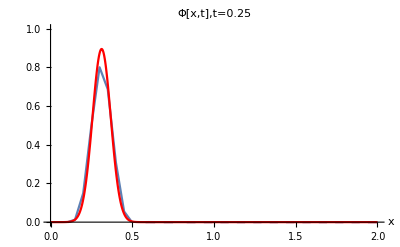
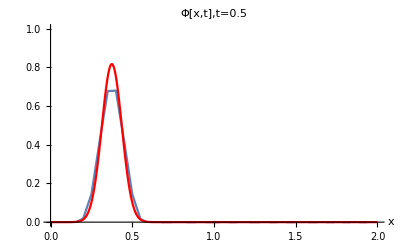
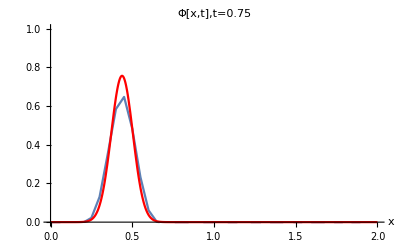
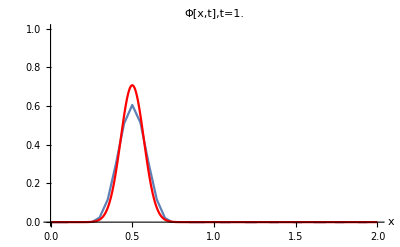
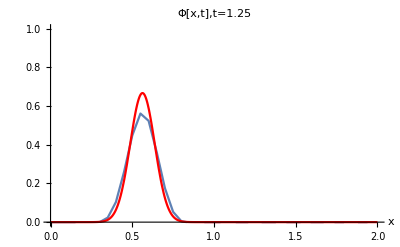
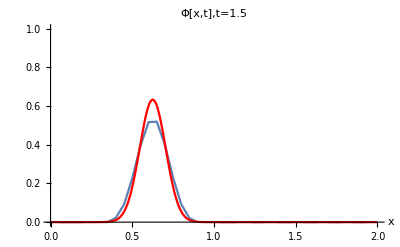
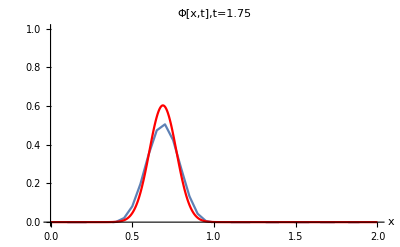

```mathematica
PetrovGalerkin = Table[ListPlot[Table[{Δx j,ϕn[j,n]},{j,0,M}]/.sol[n],
Joined->True,PlotRange->{{0,L},{0,1}},
AxesLabel->{"x",""},PlotLabel->"Φ[x,t],t="<>ToString[Δt n],
DisplayFunction->Identity],{n,0,40,5}];
exact=Table[Plot[ϕ[x,t],{x,0,L},DisplayFunction->Identity,
PlotStyle->RGBColor[1,0,0],PlotRange->{{0,L},{0,1}}],{t,0,40 Δt, 5 Δt}];
Table[Show[PetrovGalerkin[[n]],exact[[n]],DisplayFunction->$DisplayFunction],
{n,1,Length[exact]}
]
```

```mathematica
Max[Abs[Table[{ϕ[Δx j,#*Δt]-ϕn[j,#]},{j,0,M}]/.sol[#]]]& /@ Table[n,{n,0,40,5}]
```

{3.72665×10^-6,0.0723356,0.0741059,0.0956447,0.101751,0.0964416,0.0847634,0.0908788,0.0915451}

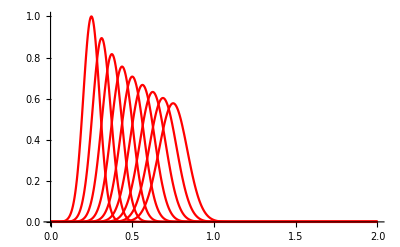

```mathematica
Show[exact,PlotRange->All]
```

Petrov Galerkin quadratic in time linear in space weights using standard shape functions :

```mathematica
Clear["Global`*"]
ϕ0[x_]:= Exp[-(x-u)^2/(4 K)];ϕ[x_,t_]:= 1/(Sqrt[1+t]) Exp[-(x-u(t+1))^2/(4 K (t+1))];
u=0.25; K=0.0125;
Δt = 0.05;M=40; Δx = L / M; L=2; u= 0.25; γ=u Δx/K; c=u Δt/Δx;
```

```mathematica
ϕn[0,n_]:=0;ϕn[M,n_]:=0;
```

```mathematica
α = Coth[γ/2]-2/γ; β=c/3-2 α/(γ c);
sol1[0] = Table[ϕn[j,0]->ϕ0[j Δx],{j,1,M-1}]
```

{ϕn[1,0]→0.449329,ϕn[2,0]→0.637628,ϕn[3,0]→0.818731,ϕn[4,0]→0.951229,ϕn[5,0]→1.,ϕn[6,0]→0.951229,ϕn[7,0]→0.818731,ϕn[8,0]→0.637628,ϕn[9,0]→0.449329,ϕn[10,0]→0.286505,ϕn[11,0]→0.165299,ϕn[12,0]→0.0862936,ϕn[13,0]→0.0407622,ϕn[14,0]→0.0174224,ϕn[15,0]→0.00673795,ϕn[16,0]→0.00235786,ϕn[17,0]→0.000746586,ϕn[18,0]→0.0002139,ϕn[19,0]→0.0000554516,ϕn[20,0]→0.0000130073,ϕn[21,0]→2.76077×10^-6,ϕn[22,0]→5.30206×10^-7,ϕn[23,0]→9.2136×10^-8,ϕn[24,0]→1.44872×10^-8,ϕn[25,0]→2.06115×10^-9,ϕn[26,0]→2.65342×10^-10,ϕn[27,0]→3.09082×10^-11,ϕn[28,0]→3.2577×10^-12,ϕn[29,0]→3.10684×10^-13,ϕn[30,0]→2.681×10^-14,ϕn[31,0]→2.09337×10^-15,ϕn[32,0]→1.47899×10^-16,ϕn[33,0]→9.45489×10^-18,ϕn[34,0]→5.46911×10^-19,ϕn[35,0]→2.86252×10^-20,ϕn[36,0]→1.35566×10^-21,ϕn[37,0]→5.80928×10^-23,ϕn[38,0]→2.2525×10^-24,ϕn[39,0]→7.90276×10^-26}

```mathematica
sol1[n_]:=Module[{vars,eqns},
(*define the variables*)
vars = Table[ϕn[j,n],{j,1,M-1}];
(* define equations substituting for the values ϕn determined at last timestep*)
eqns = Table[1/(9Δt)((ϕn[j-1,n]-ϕn[j-1,n-1])+4(ϕn[j,n]-ϕn[j,n-1])+(ϕn[j+1,n]-ϕn[j+1,n-1]))+u/(6Δx)(ϕn[j+1,n]-ϕn[j-1,n])-(α u)/(6Δx)(ϕn[j-1,n]-2ϕn[j,n]+ϕn[j+1,n])+(β u)/(6Δx)(ϕn[j-1,n]-2ϕn[j,n]+ϕn[j+1,n])+u/(6Δx)(ϕn[j+1,n-1]-ϕn[j-1,n-1])-(α u)/(6Δx)(ϕn[j-1,n-1]-2ϕn[j,n-1]+ϕn[j+1,n-1])-(β u)/(6Δx)(ϕn[j-1,n-1]-2ϕn[j,n-1]+ϕn[j+1,n-1])-K/(3 Δx^2)((ϕn[j-1,n]-2ϕn[j,n]+ϕn[j+1,n])+(ϕn[j-1,n-1]-2ϕn[j,n-1]+ϕn[j+1,n-1]))==0
,{j,1,M-1}]/.sol1[n-1];
(*solve the equations*)
Solve[eqns,vars][[1]]]
```

```mathematica
sol1[2]
```

{ϕn[1,2]→0.236178,ϕn[2,2]→0.501502,ϕn[3,2]→0.71019,ϕn[4,2]→0.858333,ϕn[5,2]→0.939652,ϕn[6,2]→0.938902,ϕn[7,2]→0.857152,ϕn[8,2]→0.715145,ϕn[9,2]→0.54539,ϕn[10,2]→0.380259,ϕn[11,2]→0.242438,ϕn[12,2]→0.141376,ϕn[13,2]→0.075426,ϕn[14,2]→0.0368281,ϕn[15,2]→0.0164633,ϕn[16,2]→0.0067412,ϕn[17,2]→0.00252978,ϕn[18,2]→0.000870663,ϕn[19,2]→0.00027504,ϕn[20,2]→0.000079828,ϕn[21,2]→0.0000213135,ϕn[22,2]→5.24243×10^-6,ϕn[23,2]→1.19003×10^-6,ϕn[24,2]→2.49834×10^-7,ϕn[25,2]→4.86318×10^-8,ϕn[26,2]→8.80381×10^-9,ϕn[27,2]→1.48744×10^-9,ϕn[28,2]→2.3551×10^-10,ϕn[29,2]→3.51078×10^-11,ϕn[30,2]→4.95316×10^-12,ϕn[31,2]→6.65112×10^-13,ϕn[32,2]→8.55088×10^-14,ϕn[33,2]→1.05884×10^-14,ϕn[34,2]→1.27018×10^-15,ϕn[35,2]→1.48406×10^-16,ϕn[36,2]→1.69688×10^-17,ϕn[37,2]→1.9064×10^-18,ϕn[38,2]→2.11141×10^-19,ϕn[39,2]→2.31431×10^-20}

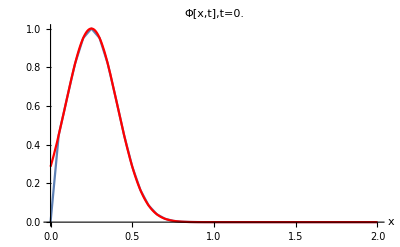
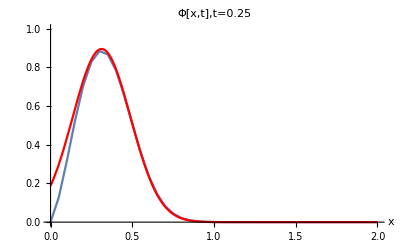
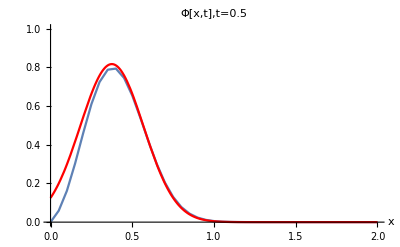
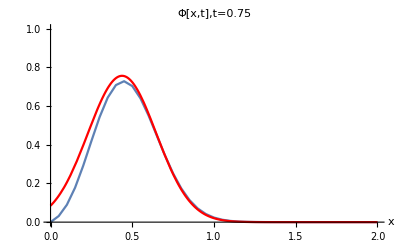
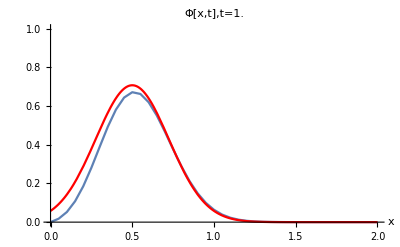
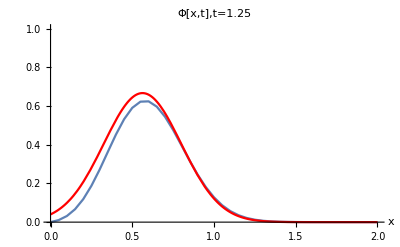
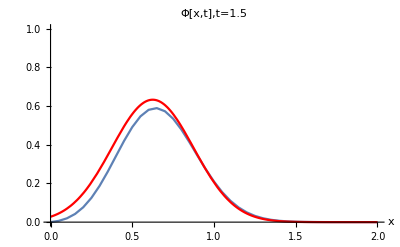
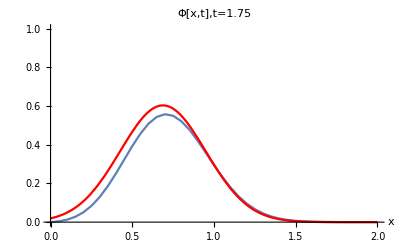

```mathematica
PetrovGalerkin2ord = Table[ListPlot[Table[{Δx j,ϕn[j,n]},{j,0,M}]/.sol1[n],
Joined->True,PlotRange->{{0,L},{0,1}},
AxesLabel->{"x",""},PlotLabel->"Φ[x,t],t="<>ToString[Δt n],
DisplayFunction->Identity],{n,0,40,5}];
exact=Table[Plot[ϕ[x,t],{x,0,L},DisplayFunction->Identity,
PlotStyle->RGBColor[1,0,0]],{t,0,40 Δt, 5 Δt}];
Table[Show[PetrovGalerkin2ord[[n]],exact[[n]],DisplayFunction->$DisplayFunction],
{n,1,Length[exact]}
]
```

```mathematica
Max[Abs[Table[{ϕ[Δx j,#*Δt]-ϕn[j,#]},{j,0,M}]/.sol1[#]]]& /@ Table[n,{n,0,40,5}]
```

{0.286505,0.187482,0.140675,0.116034,0.102358,0.0922278,0.0846025,0.079497,0.0750386}